1. NALOGA

```mathematica
GG = 9.81 ;
v0 = {10,3};
```

```mathematica
H = 10;
```

```mathematica
a = {0, -GG};
x0 = {0, H};
```

```mathematica
v[t_]:= v0 + a * t
```

```mathematica
v[4]
```

{10,-36.24}

```mathematica
x[t_]:=x0 + v0*t + a*t^2 / 2
```

```mathematica
x[3]
```

{30,-25.145}

*KOMENTAR: (* in *)*

Funkcija SlikaTocke, nariše žogo kot točko, velikosti 3% slike

```mathematica
SlikaTocke[t_]:=Point[x[t]]
Manipulate[Graphics[{SlikaTocke[t],PointSize[0.03]}, Axes -> True, PlotRange->{{0, 20},{0, 15}}], {t, 0, 3}]
```

```mathematica
Manipulate[Graphics[{SlikaTocke[t],Arrow[{{1,1},{2, 2}}]}, Axes -> True, PlotRange->{{0, 20},{0, 15}}], {t, 0, 3}]
```

```mathematica
?v
```

CloudObject`Private`v

Slika vektorja, nariše vektor hitrosti iz točke, debeline 0.5% velikosti slike

v[t_]:=v0+a t

```mathematica
SlikaVektorja[t_]:=Arrow[{x[t],x[t] + v[t]}]
```

Animacija leta žoge. Čas t premikaj o 0 do 5s.

```mathematica
Manipulate[Graphics[{SlikaVektorja[t],Thickness[0.05]}, Axes -> True, PlotRange->{{0, 20},{0, 15}}], {t, 0, 0.5}]
```

Slika žoge in vektorja po 1 sekundi.

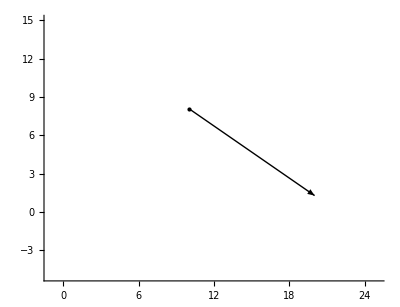

```mathematica
Graphics[{SlikaVektorja[1], SlikaTocke[1]}, Axes ->True, PlotRange->{{-1,25},{-5, 15}}, AspectRatio->Automatic]
```

Izračunaj čas padca žoge. Izračunaj še vrednost v smeri x, kjer žoga pade.

```mathematica
CasPadcaŽoge = Solve[x[t][[2]]== 0 && t > 0, t]
```

{{t→1.76604}}

```mathematica
CasLetenja = Flatten[CasPadcaŽoge][[1]]
```

t→1.76604

```mathematica
Cas = x[t]/.t-> 1.7660350319649323
```

{17.6604,0.}

```mathematica
TočkaPadcaŽoge = Cas[[1]]
```

17.6604

Žoga je padla pri 17.6604 v smeri x, padala pa je 1.76604 s.

Čas doseganja največje višine leta, ter maksimalno višino

```mathematica
Cas = Solve[v[t][[2]]== 0, t]
```

{{t→0.30581}}

```mathematica
Flatten[Cas]
```

{t→0.30581}

```mathematica
Podatki = x[t]/.t -> 0.3058103975535168
```

{3.0581,10.4587}

```mathematica
MaxVisina = Podatki[[2]]
```

10.4587

0.30581 s traja da žogica doseže najvišjo točko, ki je pri višini 10.4587

Bolj pobližana animacija leta žogice, glede na zgornje podatke

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes ->True, PlotRange->{{-1,TočkaPadcaŽoge + 1},{-1, MaxVisina + 1}}], {t, 0, 1.7660350319649323}]
```

Čas animacije je od 0 in do trenutka ko žogica pade na tla.

Kakšna je absolutna vrednost hitrosti v trenutku, ko žogica zadene tla?

```mathematica
CasLetenja = 1.7660350319649323;
```

```mathematica
Sqrt[v[CasLetenja][[1]]^2 + v[CasLetenja][[2]]^2]//N
```

17.47

Absolutno vrednosz hitrosti sem izračunala kot absolutno vrednost vektorja.

2. NALOGA

```mathematica
?Hyperplane
```

Hyperplane[n,p] represents the hyperplane with normal n passing through the point p.
Hyperplane[n,c] represents the hyperplane with normal n given by the points x that satisfy n.x==c.

```mathematica
r111 = Ravnina[{-1, -1, -1},{1,1,1}];
```

```mathematica
Slika[Ravnina[n_, v_]]:= Hyperplane[n, v]
```

```mathematica
?Format
```

Format[expr] prints as the formatted form of expr. Assigning values to Format[expr] defines print forms for expressions. 
Format[expr,form] gives a format for the specified form of output.

```mathematica
Format[r_Ravnina]:=Graphics3D[Slika[r]]
```

```mathematica
Format[r111]
```

-Graphics3D-

Funkciji ki vrneta točko in normalo ravnine

```mathematica
Tocka[Ravnina[n_, v_]]:=v
```

```mathematica
Normala[Ravnina[n_,v_]]:=n
```

```mathematica
Tocka[Ravnina[{-1, -1, -1},{1,1,1}]]
```

{1,1,1}

```mathematica
Normala[Ravnina[{-1, -1, -1},{1,1,1}]]
```

{-1,-1,-1}

Definiraj koordinatne ravnine rx, ry, rz, ki gredo skozi točko 0 in so njihove normale enotski
vektorji koordinatnih osi.

```mathematica
rx = Ravnina[{1,0,0},{0,0,0}];
ry = Ravnina[{0,1,0},{0,0,0}];
rz = Ravnina[{0,0,1},{0,0,0}];
```

Sestavi funkcijo SlikaNormale[Ravnina[n_, v_]], ki vrne grafični objekt slike normale. Uporabi
grafični objekt Arrow.

```mathematica
SlikaNormale[Ravnina[n_, v_]]:= Arrow[{v, v + n}]
Format[r_Ravnina]:=Graphics3D[{SlikaNormale[r], Slika[r]}]
```

```mathematica
Format[r111]
```

-Graphics3D-

```mathematica
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

Nariši vse štiri ravnine rx, ry, rz, r111 na isti sliki skupaj z normalami

```mathematica
ravnine = {r111,rx,ry,rz};
```

```mathematica
Graphics3D[Map[{Slika[#],SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

Sestavi funkcijo Enacba[Ravnina[n_, v_]], ki vrne enačbo ravnine.

```mathematica
ClearAll[x,y,z]
```

```mathematica
Enacba[Ravnina[n_,v_]]:=n[[1]]*x+n[[2]]*y+n[[3]]*z == n[[1]]*v[[1]]+n[[2]]*v[[2]]+n[[3]]*v[[3]]
```

```mathematica
Enacba[r111]
```

-x-y-z==-3

Sestavi funkcijo ResiSistem[sistem_List], ki za dan sistem treh enačb v spremenljivkah x, y
in z vrne točko rešitve. Predpostavi, da je sistem takšen, da vrne samo eno rešitev.

```mathematica
ResiSistem[sistem_List]:= Solve[sistem[[1]], sistem[[2]], sistem[[3]], {x,y,z}]
```

3. NALOGA

Izberi si neko 3D telo in ga nariši s pomočjo točk in poligonov. Narišite tudi normalo nad eno ploskvijo, ki gleda ven iz telesa iz težišča ploskve.

Narisala bom nekaj vzporednih ravnin. In ravnino v obliki trikotnika ki seka preko vseh ravnin.

```mathematica
ravnina1 = Ravnina[{1, 1, 1},{1,1,1}];
ravnina2 = Ravnina[{2, 2, 2},{2,2,2}];
ravnina3 = Ravnina[{3, 3, 3},{3,3,3}];
ravnina4 = Ravnina[{4,4,4},{4,4,4}];
```

```mathematica
podaneRavnine = {ravnina1, ravnina2, ravnina3, ravnina4};
```

```mathematica
SlikeRavnin = Graphics3D[Map[{Slika[#],SlikaNormale[#], Polygon[{{1,2,3},{5,-4,-6},{12,15,16}}] }&, podaneRavnine]]
```

-Graphics3D-